# Coauthor Network Analysis: Investigation into Endnote Bibliographic Data

## Wang Chengjun

## 20110507@HALL 8

http : // mathgis.blogspot.com/2010/04/play - with - bibliographic - data.html

## Data Clean

### Imort xml data

```mathematica
xml=Import["D:/Jonathan's COM8005/IMC/imc review.xml"]; 
(*note: in this way, you can add your annotation*)
```

### Get authors information

```mathematica
authors=Cases[xml,XMLElement["authors",_,authors_]->authors,Infinity];
```

```mathematica
names=Cases[#,XMLElement["author",_,{XMLElement["style",_,name_]}]->name]&/@authors;
(*in this case, no need to flatten so i fix the flatten level as 0*)
```

```mathematica
Length[names]
```

6848

### Caculate the distribution

```mathematica
table=Sort[Tally[Length[#]&/@names],#1[[1]]<#2[[1]]&]
```

{{0,6848}}

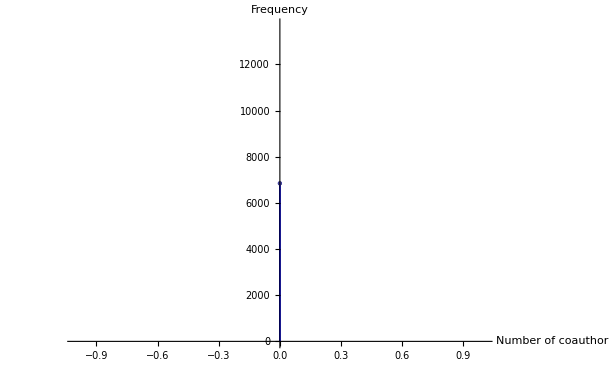

```mathematica
ListPlot[table,Filling->Axis,FillingStyle->Blue,AxesLabel->{"Number of coauthor","Frequency"}]
```

### Split the coauthors

```mathematica
split=SplitBy[#,".,"]&/@Sort[names];
```

### Permutations of co-author

```mathematica
Permutations[#,{2}]&/@split;(*however, if the length is smaller than 2, it will be blank*)
```

### GraphPlot

```mathematica
Length[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}]]
```

0

```mathematica
GraphPlot[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}]]
```

-Graphics-